```mathematica
GraphData[5]
```

{2P2+K1,BannerGraph,{Beineke,2},BullGraph,ButterflyGraph,C3+2K1,C3+P2,C4+K1,{CompleteBipartite,{2,3}},{CompleteTripartite,{1,1,3}},CricketGraph,{Cycle,5},DartComplementGraph,DartGraph,{Dipyramid,3},{Empty,5},ForkGraph,GemGraph,HouseGraph,HouseXGraph,K1,3+K1,K4-e+K1,K4+K1,KiteGraph,{Lollipop,{4,1}},P2+3K1,P3+2K1,P3+P2,P4+K1,{Path,5},PentatopeGraph,{Star,5},{Tadpole,{3,2}},{Wheel,5}}

```mathematica
GraphData["BullGraph", "Genus"]
```

0

```mathematica
Select[GraphData[10], MissingQ[GraphData[#, "Genus"]] &]
```

{{Circulant,{10,{1,2,4}}},{Circulant,{10,{1,2,5}}},{Circulant,{10,{1,4,5}}},{Circulant,{10,{1,2,3,5}}},{Circulant,{10,{1,2,4,5}}},{CompleteKPartite,{1,1,1,7}},{CompleteKPartite,{2,2,3,3}},{CompleteKPartite,{1,1,2,2,2,2}},{CompleteKPartite,{1,1,1,1,2,2,2}},{CompleteKPartite,{1,1,1,1,1,1,2,2}},{CompleteKPartite,{1,1,1,1,1,1,1,1,2}},{CompleteTripartite,{1,2,7}},{CompleteTripartite,{1,3,6}},{CompleteTripartite,{1,4,5}},{CompleteTripartite,{2,3,5}},{CompleteTripartite,{3,3,4}},{Cone,{5,5}},{Cone,{6,4}},{Cone,{7,3}},{Fan,{3,7}},{Fan,{4,6}},{Fan,{5,5}},NechushtanGraph,{PathComplement,10},{Queen,{2,5}},{Quintic,{10,1}},{Quintic,{10,2}},{Quintic,{10,4}},{Quintic,{10,5}},{Quintic,{10,6}},{Quintic,{10,7}},{Quintic,{10,8}},{Quintic,{10,9}},{Quintic,{10,10}},{Quintic,{10,11}},{Quintic,{10,12}},{Quintic,{10,14}},{Quintic,{10,15}},{Quintic,{10,16}},{Quintic,{10,17}},{Quintic,{10,18}},{Quintic,{10,19}},{Quintic,{10,20}},{Quintic,{10,21}},{Quintic,{10,22}},{Quintic,{10,23}},{Quintic,{10,24}},{Quintic,{10,25}},{Quintic,{10,26}},{Quintic,{10,27}},{Quintic,{10,28}},{Quintic,{10,29}},{Quintic,{10,30}},{Quintic,{10,31}},{Quintic,{10,32}},{Quintic,{10,33}},{Quintic,{10,34}},{Quintic,{10,35}},{Quintic,{10,36}},{Quintic,{10,37}},{Quintic,{10,38}},{Quintic,{10,39}},{Quintic,{10,40}},{Quintic,{10,41}},{Quintic,{10,42}},{Quintic,{10,43}},{Quintic,{10,44}},{Quintic,{10,45}},{Quintic,{10,46}},{Quintic,{10,47}},{Quintic,{10,48}},{Quintic,{10,49}},{Quintic,{10,50}},{Quintic,{10,51}},{Quintic,{10,52}},{Quintic,{10,54}},{Quintic,{10,55}},{Quintic,{10,56}},{Quintic,{10,57}},{Quintic,{10,58}},{Rook,{2,5}},{Septic,{10,1}},{Septic,{10,2}},{Septic,{10,4}},{Sextic,{10,1}},{Sextic,{10,2}},{Sextic,{10,3}},{Sextic,{10,4}},{Sextic,{10,5}},{Sextic,{10,6}},{Sextic,{10,9}},{Sextic,{10,10}},{Sextic,{10,11}},{Sextic,{10,12}},{Sextic,{10,13}},{Sextic,{10,14}},{Sextic,{10,15}},{Sextic,{10,16}},{Sextic,{10,17}},{Sextic,{10,21}},{Triangular,5},{TriangularHoneycombQueen,4}}

{BipartiteKneser,{11,3}}

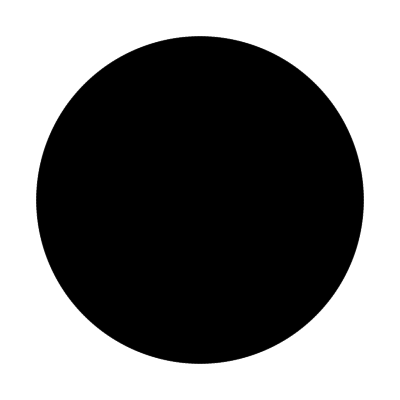

```mathematica
g = {"BipartiteKneser", {11, 3}}
plot = GraphPlot[GraphData[g], VertexStyle -> Directive[Black, PointSize[Large]], EdgeStyle -> Black, PlotStyle -> Black]
```

```mathematica
GraphData[g, "Genus"]
EdgeCount[GraphData[g]]
```

Missing[NotAvailable]

9240

```mathematica
PlanarGraphQ[g]
```

False

```mathematica
Export["/Users/alex/Desktop/People/Austin/Genus/Balaban10/BipartiteKneser11-3.pdf", plot]
```

/Users/alex/Desktop/People/Austin/Genus/Balaban10/BipartiteKneser11-3.pdf

```mathematica
Export["/Users/alex/Desktop/People/Austin/Genus/PAGE/adjacency_lists/bipartite-kneser12-5.txt", AdjacencyList[GraphData[g]], "Text"]
```

/Users/alex/Desktop/People/Austin/Genus/PAGE/adjacency_lists/bipartite-kneser12-5.txt

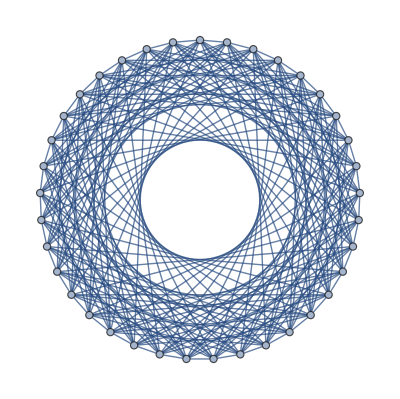

```mathematica
GraphData[{"Cyclotomic", 37}]
```

```mathematica
Select[GraphData["BipartiteKneser"], MissingQ[GraphData[#, "Genus"]] &]
```

{{BipartiteKneser,{6,2}},{BipartiteKneser,{7,2}},{BipartiteKneser,{8,2}},{BipartiteKneser,{8,3}},{BipartiteKneser,{9,2}},{BipartiteKneser,{9,3}},{BipartiteKneser,{10,2}},{BipartiteKneser,{10,3}},{BipartiteKneser,{10,4}},{BipartiteKneser,{11,2}},{BipartiteKneser,{11,3}},{BipartiteKneser,{11,4}},{BipartiteKneser,{12,2}},{BipartiteKneser,{12,3}},{BipartiteKneser,{12,4}},{BipartiteKneser,{12,5}},{Crown,6},{Crown,7},{Crown,8},{Crown,9},{Crown,10},{Crown,11},{Crown,12},{Crown,13},{Crown,14},{Crown,15},{Crown,16},{Crown,17},{Crown,18},{Crown,19},{Crown,20},DanzerGraph,{MiddleLayer,4},{MiddleLayer,5}}